# octet.experiment.rencon1.figure.lambda-merge.style-1.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.paper.chpt.ed9\octet.experiment.rencon1.figure.lambda-merge.style-1.nb

this nb is to record the octet ge gm experiment data.

## initial

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
fig`calc`nucleon`ge`u = {0, 0, 0};
fig`calc`nucleon`ge`d = {0, 0, 0};
fig`calc`nucleon`ge`s = {0, 0, 0};
```

```mathematica
fig`calc`nucleon`gm`u = {0, 0, 0};
fig`calc`nucleon`gm`d = {0, 0, 0};
fig`calc`nucleon`gm`s = {0, 0, 0};
```

```mathematica
style`exp={
RGBColor[0.368417,0.506779,0.709798]->Blue,
AbsoluteThickness[_]-> AbsoluteThickness[0.5],
PointSize[_]->PointSize[0.02]
};
```

```mathematica
style`calc={
AbsoluteThickness[_]-> AbsoluteThickness[0.5]
};
```

## nucleon`ge`light-sea

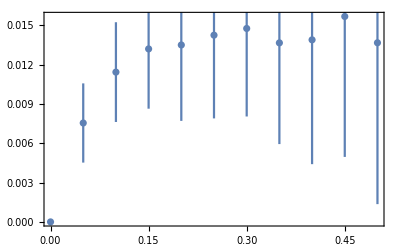
```mathematica
fig`exp`nucleon`ge`lightsea=
-Graphics-/.style`exp;
```

## fig`calc`nucleon`ge`u

```mathematica
fig`calc`nucleon`ge`u⟦1⟧=(*Λ==0.80 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ1";
```

```mathematica
fig`calc`nucleon`ge`u⟦2⟧=(*Λ==0.90 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ2";
```

```mathematica
fig`calc`nucleon`ge`u⟦3⟧=(*Λ==1.00 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ3";
```

## fig`calc`nucleon`ge`d

```mathematica
fig`calc`nucleon`ge`d⟦1⟧=
-Graphics-;
```

```mathematica
fig`calc`nucleon`ge`d⟦2⟧=
-Graphics-;
```

```mathematica
fig`calc`nucleon`ge`d⟦3⟧=
-Graphics-;
```

## fig`comparison`ge`u

```mathematica
fig`comparison`ge`u=Show[
{fig`exp`nucleon`ge`lightsea,fig`calc`nucleon`ge`u⟦1⟧,fig`calc`nucleon`ge`u⟦2⟧,fig`calc`nucleon`ge`u⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Ge(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

## nucleon`ge`strange

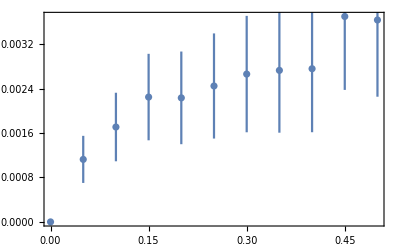
```mathematica
fig`exp`nucleon`ge`s=
-Graphics-/.style`exp;
```

## fig`calc`nucleon`ge`s

```mathematica
fig`calc`nucleon`ge`s⟦1⟧=(*Λ==0.80 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ1";
```

```mathematica
fig`calc`nucleon`ge`s⟦2⟧=(*Λ==0.90 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ2";
```

```mathematica
fig`calc`nucleon`ge`s⟦3⟧=(*Λ==1.00 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ3";
```

## fig`comparison`ge`s

```mathematica
fig`comparison`ge`s=Show[
{fig`exp`nucleon`ge`s,fig`calc`nucleon`ge`s⟦1⟧,fig`calc`nucleon`ge`s⟦2⟧,fig`calc`nucleon`ge`s⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Ge(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

## nucleon`gm`lightsea

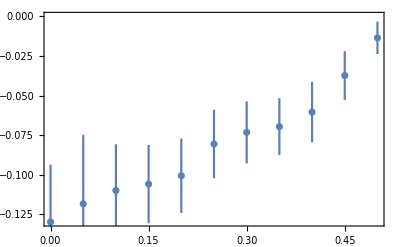
```mathematica
fig`exp`nucleon`gm`lightsea=
-Graphics-/.style`exp;
```

## fig`calc`nucleon`gm`u

```mathematica
fig`calc`nucleon`gm`u⟦1⟧=(*Λ==0.80 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ1";
```

```mathematica
fig`calc`nucleon`gm`u⟦2⟧=(*Λ==0.90 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ2";
```

```mathematica
fig`calc`nucleon`gm`u⟦3⟧=(*Λ==1.00 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ3";
```

## fig`calc`nucleon`gm`d

```mathematica
fig`calc`nucleon`gm`d⟦1⟧=
-Graphics-;
```

```mathematica
fig`calc`nucleon`gm`d⟦2⟧=
-Graphics-;
```

```mathematica
fig`calc`nucleon`gm`d⟦3⟧=
-Graphics-;
```

## fig`comparison`gm`u

```mathematica
fig`comparison`gm`u=Show[
{fig`exp`nucleon`gm`lightsea,fig`calc`nucleon`gm`u⟦1⟧,fig`calc`nucleon`gm`u⟦2⟧,fig`calc`nucleon`gm`u⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

## nucleon`gm`strange

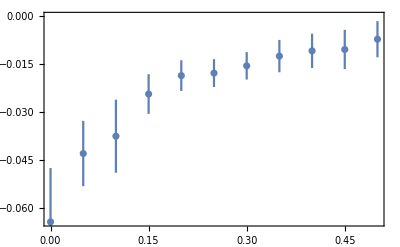
```mathematica
fig`exp`nucleon`gm`s=-Graphics-/.style`exp;
```

## fig`calc`nucleon`gm`s

```mathematica
fig`calc`nucleon`gm`s⟦1⟧=(*Λ==0.80 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ1";
```

```mathematica
fig`calc`nucleon`gm`s⟦2⟧=(*Λ==0.90 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ2";
```

```mathematica
fig`calc`nucleon`gm`s⟦3⟧=(*Λ==1.00 Gev*)
-Graphics-/.style`calc/."Loop"->"Λ3";
```

```mathematica
fig`comparison`gm`s=Show[
{fig`exp`nucleon`gm`s,fig`calc`nucleon`gm`s⟦1⟧,fig`calc`nucleon`gm`s⟦2⟧,fig`calc`nucleon`gm`s⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

## paper`show

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

u

```mathematica
fig`sea`u=Labeled[
GraphicsGrid[
{{fig`comparison`ge`u(*/.(ImagePadding->_)->(ImagePadding->All)*)(*fig`comparison`ge`u*),fig`comparison`gm`u}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->Automatic,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"light-sea, Ge (left side) and Gm (right side)"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

-Graphics-light-sea, Ge (left side) and Gm (right side)

d

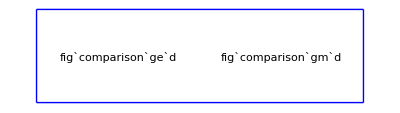
-Graphics-sea d

```mathematica
fig`sea`d=Labeled[
GraphicsGrid[
{{fig`comparison`ge`d/.(ImagePadding->_)->(ImagePadding->All)(*fig`comparison`ge`u*),fig`comparison`gm`d}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"sea d"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]/.{AbsoluteThickness[_]-> AbsoluteThickness[0.5],PointSize[_]->PointSize[0.02]}
```

s

```mathematica
fig`sea`s=Labeled[
GraphicsGrid[
{{fig`comparison`ge`s,fig`comparison`gm`s}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->Automatic,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"strange, Ge (left side) and Gm (right side)"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

-Graphics-strange, Ge (left side) and Gm (right side)

export

```mathematica
SetDirectory["C:\\Users\\Tom\\Desktop\\octet.paper.ed4"];
```

```mathematica
Export["fig.sea.u.eps",fig`sea`u];
(*Export["fig.sea.d.eps",fig`sea`d];*)
Export["fig.sea.s.eps",fig`sea`s];
```